```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/Documents/Courses/MATH161/Notes/7-Continuity

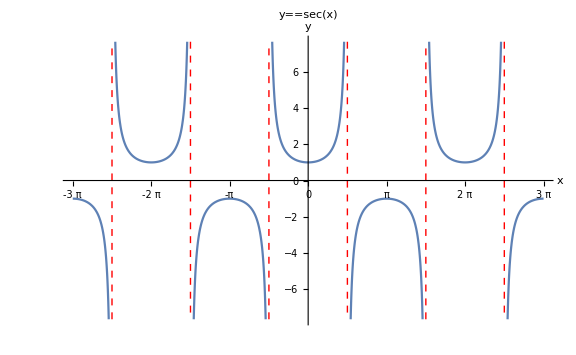

sec.png

```mathematica
f[x_]=Sec[x];
{a,b}={-3*Pi,3*Pi};
plt=Plot[f[x],{x,a,b},PlotLabel->y==f[x],AxesLabel->{x,y},ImageSize->Large,ExclusionsStyle->{{Red,Dashed}},Ticks->{Table[n*Pi/2,{n,-6,6}],Automatic}]
Export["sec.png",plt]
```